```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/ece1229-antenna" ] 

fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/ece1229-antenna

```mathematica
Manipulate[ 
Plot[ChebyshevT[n, z0 x], {x, -r, r}, AxesLabel -> { "x", Row[{"T_n(z_0x) = ", TraditionalForm[ChebyshevT[n, z0 x]]}]
}
, PlotRange -> {{-r, r}, {-r, r}}
, Epilog -> {
(*Color -> Red,*)
PointSize -> Large,
Point[{1, ChebyshevT[n, z0 ]}],
Point[{-1, ChebyshevT[n, -z0 ]}]
}
],
{n, 1, 10, 1, Appearance->"Labeled"},
{{z0, 1, "z_0"}, 1, 5, Appearance->"Labeled"},
{{r, 1, "scale"}, 1, 10, Appearance->"Labeled"} ]
```

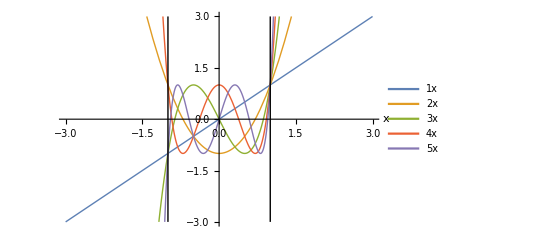

```mathematica
ChebyChevOneToFiveFig1 = With[{r = 3, z0 = 1, n = 5},
Plot[ChebyshevT[#, z0 x]& /@ Range[n] // Evaluate, {x, -r, r}, AxesLabel -> { "x"(*, "T_n(x)"*) } 
, PlotRange -> {{-r, r}, {-r, r}}
, PlotStyle->Thick
, Epilog -> {
Line[{{1,-r}, {1, r}}],
Line[{{-1,-r}, {-1, r}}]
}
, PlotLegends->Placed[ Row[{HoldForm[TraditionalForm[ChebyshevT[#, x] ]]
(*, " = ", TraditionalForm[ChebyshevT[#, x] ]*)
} ] &/@ Range[n], {Right,Bottom} ]
]]
```

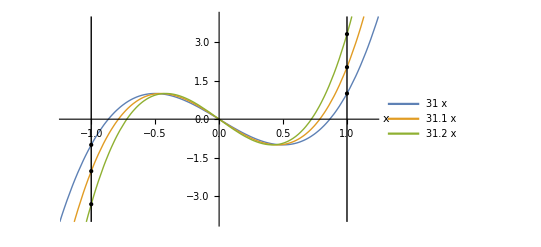

```mathematica
ChebyChevThreeScaledFig2 = With[{r = 4, n = 3, z0 = {1,1.1, 1.2}},
Plot[ChebyshevT[n, # x]& /@z0 // Evaluate, {x, -r, r}, AxesLabel -> { "x"(*, "T_n(x)"*) } 
, PlotRange -> {{-1.2, 1.2}, {-r, r}}
, PlotStyle-> Thick
, Epilog -> {
Flatten[{
Line[{{1,-r}, {1, r}}],
Line[{{-1,-r}, {-1, r}}],
PointSize -> Medium,
Point[{1, ChebyshevT[n, # ]}] &/@ z0,
Point[{-1, ChebyshevT[n, -# ]}] &/@ z0
}
]
}
, PlotLegends->Placed[ Row[{HoldForm[TraditionalForm[ChebyshevT[n, #x] ]]
(*, " = ", TraditionalForm[ChebyshevT[#, x] ]*)
// fs} ] &/@z0, {Left,Top} ]
]]
```

```mathematica
peeters`exportForLatex["ChebyChevOneToFiveFig1", ChebyChevOneToFiveFig1]
peeters`exportForLatex["ChebyChevThreeScaledFig2", ChebyChevThreeScaledFig2]
```

{ChebyChevOneToFiveFig1.eps,ChebyChevOneToFiveFig1pn.png}

{ChebyChevThreeScaledFig2.eps,ChebyChevThreeScaledFig2pn.png}